```mathematica
(* Generate a skew normal distribution. *)
dist = SkewNormalDistribution[1.052209643,1.451601,-2.173758];
```

```mathematica
(* Get its mean, variance, and skewness for refrence *)

Dataset[{
{"Mean",Chop[Mean@dist, 10^-9]},
{"Variance",Variance@dist}, 
{"Skew", Skewness@dist},
{"Lower 2.5% tail quantile", Quantile[dist, 0.025]},
{"Upper 2.5% tail quantile", Quantile[dist, 0.975]}}]
```

0.274829 ⅇ^(-0.237288 (-1.0522+x)^2) Erfc[1.05889 (-1.0522+x)]

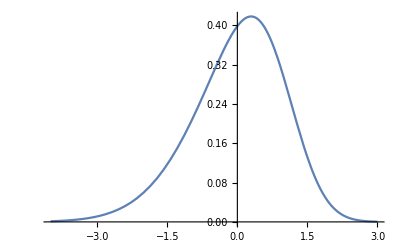

```mathematica
(* Get and plot its PDF *)
PDF[SkewNormalDistribution[1.0522009,1.451601,-2.173758],x]
Plot[%, {x, -4, 3}]
```

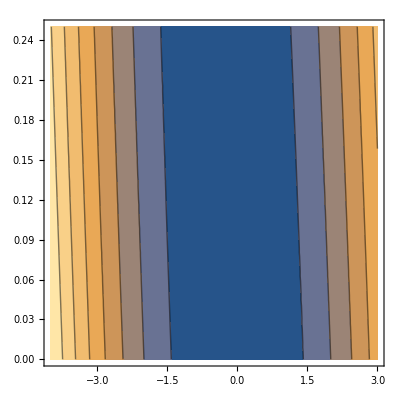

```mathematica
(* Define cost function and plot its contours *)
ContourPlot[u^2+(w+u)^2, {w, -4, 3}, {u, 0, 0.25}]
```

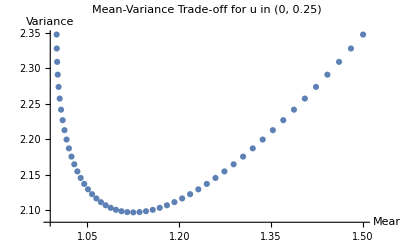

```mathematica
(* Explore mean-variance tradeoff for u in (0, 0.5) *)
umin = 0.00; umax = 0.5; du = 0.01; 
means = Table[Mean@TransformedDistribution[u^2+(W+u)^2, W \[Distributed] dist], {u,umin,umax,du}];
variances = Table[Variance@TransformedDistribution[u^2+(W+u)^2, W \[Distributed] dist], {u,umin,umax,du}];

ListPlot[Transpose@{means,variances}, PlotLabel-> "Mean-Variance Trade-off for u in (0, 0.25)",
Axes-> True, AxesLabel -> {"Mean", "Variance"}]
```

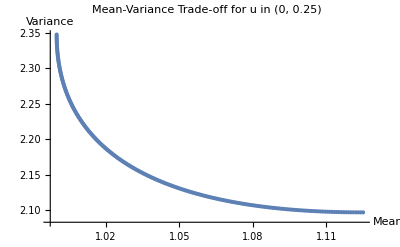

```mathematica
(* Explore mean-variance tradeoff for u in (0, 0.25); we only care about region where there is a trade-off between mean and variance. For u > 0.25, both mean and variance are increasing.*)
umin = 0.00; umax = 0.25; du = 0.001; 
means = Table[Mean@TransformedDistribution[u^2+(W+u)^2, W \[Distributed] dist], {u,umin,umax,du}];
variances = Table[Variance@TransformedDistribution[u^2+(W+u)^2, W \[Distributed] dist], {u,umin,umax,du}];
controls = Table[u, {u, umin, umax, du}];
ListPlot[Transpose@{means,variances}, PlotLabel-> "Mean-Variance Trade-off for u in (0, 0.25)",
Axes-> True, AxesLabel -> {"Mean", "Variance"}]
```

```mathematica
(* Export results to .mat files for import into Matlab *)
Export[NotebookDirectory[]<>"skewnormal_example_means.mat", means];
Export[NotebookDirectory[]<>"skewnormal_example_variances.mat", variances]; 
Export[NotebookDirectory[]<>"skewnormal_example_controls.mat", controls];
```

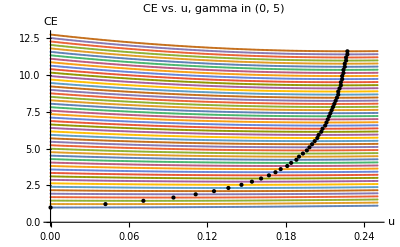

```mathematica
(* Plot certainty equivalents for theta in (0, 5) *)
certaintyEquivalents = Table[means+theta*variances,{theta, 0, 5, 0.1}];
minimumCE = Table[Min[certaintyEquivalents[[i,All]]], {i, 1, Length[certaintyEquivalents]}];
controlMinimumCE = Table[controls[[Ordering[certaintyEquivalents[[i,All]],1]]], {i, 1, Length[certaintyEquivalents]}];

ListPlot[TemporalData[certaintyEquivalents, {controls}], Epilog-> {PointSize[Medium], Point[Transpose[{Flatten[controlMinimumCE], minimumCE}]]},
PlotLabel-> "CE vs. u, gamma in (0, 5)",
Axes-> True, AxesLabel -> {"u", "CE"}]
```

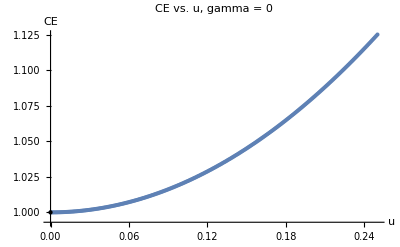

```mathematica
(* plot an individual curve for gamma = 0 *)
(* note: tricked the table iterator to only look at gamma = 0 *)
certaintyEquivalents = Table[means+theta*variances,{theta, 0, 5, 10}];
minimumCE = Table[Min[certaintyEquivalents[[i,All]]], {i, 1, Length[certaintyEquivalents]}];
controlMinimumCE = Table[controls[[Ordering[certaintyEquivalents[[i,All]],1]]], {i, 1, Length[certaintyEquivalents]}];

ListPlot[TemporalData[certaintyEquivalents, {controls}], Epilog-> {PointSize[Medium], Point[Transpose[{Flatten[controlMinimumCE], minimumCE}]]},
PlotLabel-> "CE vs. u, gamma = 0",
Axes-> True, AxesLabel -> {"u", "CE"}]
```

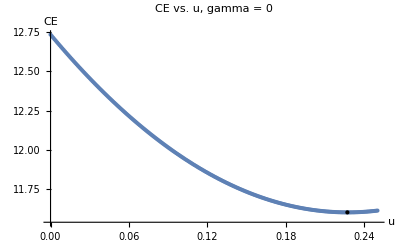

```mathematica
(* plot an individual curve for gamma = 5 *)
(* note: tricked the table iterator to only look at gamma = 5 *)
certaintyEquivalents = Table[means+theta*variances,{theta, 5, 6, 10}];
minimumCE = Table[Min[certaintyEquivalents[[i,All]]], {i, 1, Length[certaintyEquivalents]}];
controlMinimumCE = Table[controls[[Ordering[certaintyEquivalents[[i,All]],1]]], {i, 1, Length[certaintyEquivalents]}];

ListPlot[TemporalData[certaintyEquivalents, {controls}], Epilog-> {PointSize[Medium], Point[Transpose[{Flatten[controlMinimumCE], minimumCE}]]},
PlotLabel-> "CE vs. u, gamma = 0",
Axes-> True, AxesLabel -> {"u", "CE"}]
```

```mathematica
(* draw 100,000 samples for u in (0, 0.25) by 0.001 *)
costDistributions = Table[SeedRandom[0];RandomVariate[TransformedDistribution[u^2+(W+u)^2, W \[Distributed] dist],100000], {u,umin,umax,du}];
Table[Export[NotebookDirectory[]<>"/samples/skewnormal_example_phi_1E5_samples_"<>ToString[i]<>".mat", costDistributions[[i,All]], "Version"->"7.3"], {i, 1,  Length[costDistributions], 1}];
```

```mathematica
(* draw 10E7 samples for u = 0 and u = 0.25 *)
costDistributions = Table[SeedRandom[0];RandomVariate[TransformedDistribution[u^2+(W+u)^2, W \[Distributed] dist],10000000], {u,umin,umax,0.25}];
Table[Export[NotebookDirectory[]<>"/samples/skewnormal_example_phi_1E7_samples_"<>ToString[i]<>".mat", costDistributions[[i,All]], "Version"->"7.3"], {i, 1,  Length[costDistributions], 1}];
```